The equation that we want to solve is
θ''[r]+2/r θ'[r]+(ω^2-1)θ[r]==0
which can be cast in the following form
1/r d^2/dr^2(r θ[r])+(ω^2-1)θ[r]==0
and with the ansatz θ[r]=χ[r]/r we obtain
d^2/dr^2 χ[r]+(ω^2-1)χ[r]==0
This is the Schroedinger equation in spherical symmetry for a free particle with l=0 and negative energy. The general solution of this equation is
χ[r]=χ_+E^(√(1-ω^2)r)+χ_-E^(-√(1-ω^2)r)
The boundary condition χ[r]→0 for r→∞ translates into
χ[r]=χ_-E^(-√(1-ω^2)r)
With an extra term on the RHS the equation becomes
d^2/dr^2 χ[r]+(ω^2-1)χ[r]==r C[r]
and the complete solution is
χ_c[r]=χ_-E^(-√(1-ω^2)r)+χ_p[r]
where
d^2/dr^2 χ_p[r]+(ω^2-1)χ_p[r]==r C[r]
and then, if C[r]=C, χ_p must be linear in r
χ_p[r]==C/(ω^2-1)r
The final solution is then
θ[r]=(χ_-)/r E^(-√(1-ω^2)r)+C/(ω^2-1)
Below I prove that this is indeed the solution calculated by Mathematica

```mathematica
χm=0.1;
ω=0.8;
cc=0.;
rmax=5;
rmin=0.1;
th[r_]:=χm/r E^(-√(1-ω^2)r)+cc/(ω^2-1);
thprime[r_]:=-(E^(-r √(1-ω^2)) χm)/r^2-(E^(-r √(1-ω^2)) χm √(1-ω^2))/r;
sol=NDSolve[{θ''[r]+2/r θ'[r]+(ω^2-1)θ[r]==cc,θ[rmax]==th[rmax],θ'[rmax]==thprime[rmax]},θ[r],{r,rmin,rmax}];
θs[r_]=θ[r]/.sol;
```

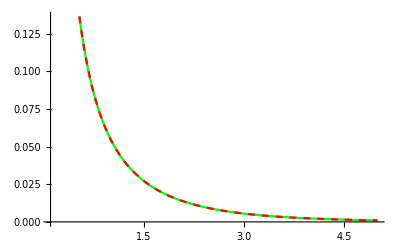

```mathematica
Plot[{θs[r],th[r]},{r,rmin,rmax},PlotStyle->{Green,{Red,Dashed}}]
```

Gravity cannot be neglected, then
θ''[r]+2/r θ'[r]+(ω^2-1+2ϕ)θ[r]==C
where in a mean field approximation
ϕ=-k_G/2 1/r
and then
θ''[r]+2/r θ'[r]+(ω^2-1-k_G/r)θ[r]==C
(*****************************************************************************
Rewriting it in terms of θ[r]=χ[r]/r,
d^2/dr^2 χ[r]+(ω^2-1-k_G/r)χ[r]==C r
for r→0 the solution of the simplified equation
d^2/dr^2 χ[r]-k_G/r χ[r]=0
is a Bessel function
χ=χ_1 √(k_G r)I_1(2 √(k_G r))+χ_2 √(k_G r)K_1(2 √(k_G r))
And for large radii, assuming that C vanishes at infinity, we recover the exponential solutions of the first case (solutions of d^2/dr^2 χ[r]+(ω^2-1)χ[r]==0)
******************************************************************************)
The stability of the clump can be described by this equation, which sounds like a stationary Schroedinger equation with (1-ω^2) as energy
θ''[r]+2/r θ'[r]-k_G/r θ[r]-C==(1-ω^2)θ[r]
assuming an exponential ansatz (because C vanishes somewhere at infinity)
θ[r]=θ_0 E^(-r/R)
the Hamiltonian is easily identified as (the Hertzberg's one plus the C term coming from -g_aγ E·B∫d^3 x θ)
H_eff=N/(2 R^2)-(5 N^2)/(16 R)-N^2/(128π R^3)-2C R^3
Extremizing for R we have
0=-R+(5N)/16 R^2+(3N)/(128π)-(6C R^6)/N
Which is solved below to give the stability radii

```mathematica
n=9;
c=10;
Print["c≠0 case, note the presence of another (un)stable solution depending on the sign of c"]
NSolve[-R+(5n)/16 R^2+(3n)/(128π)-(6c R^6)/n==0,R]
Print["c=0 case"]
8./(5n)-(√(512π-15 n^2))/(10 √(2π)n)
8./(5n)+(√(512π-15 n^2))/(10 √(2π)n)
```

c≠0 case, note the presence of another (un)stable solution depending on the sign of c

{{R→-0.881907},{R→-0.0839185-0.820989 ⅈ},{R→-0.0839185+0.820989 ⅈ},{R→0.0898406},{R→0.270881},{R→0.689023}}

c=0 case

0.0898477

0.265708

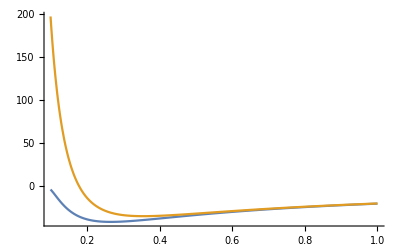

```mathematica
n=9;
c=0;
H[n_,c_,r_,d_]:=n/(2 r^2)-5/16 n^2/r-d n^2/(128π r^3)-2c r^(3/2);
Plot[{H[n,c,r,1],H[n,c,r,0]},{r,0.1,1},PlotRange->All]
```

The complete Lagrangian is
L=i/2(ψ̇ ψ^*-ψ(ψ̇)^*)-1/(2m)∇ψ^*∇ψ-m ψ^*ψ ϕ+(ψ^(*2)ψ^2)/(16 f_a^2)+g_aγ ψ E·B
The momentum of ψ is
i/2 ψ^*
and the Hamiltonian reads
H=∫d^3 x(1/(2m)∇ψ^*∇ψ+m ψ^*ψ ϕ-(ψ^(*2)ψ^2)/(16 f_a^2)-g_aγ ψ E·B)
ϕ=-(G m)/2∫d^3 x' (ψ^*(x')ψ(x'))/(|x-x'|)
The time independent solution can be written as
ψ=Ψ E^(-i μ t)
and then
H_kin=(2π)/m∫dr r^2(dΨ/dr)^2
H_int=-π/(4 f_a^2)∫dr r^2 Ψ^4
H_G=-(G m^2)/2(4π)^2∫dr r^2∫dr' r^('2)(Ψ(r)^2 Ψ(r')^2)/(|r-r'|)=-2π G m^2 N∫dr r Ψ(r)^2
<H_EM>=-(4π g_aγ)/(√(2m))∫dr r^2 Ψ ((∫_0)^T dt E^(-i μ t)(E·B)(t))/T=-√(2/m)π g_aγ∫dr r^2 Ψ F_EM(r)
Using the exponential ansatz
Ψ=√(N/(π R^3))E^(-r/R)
and the energy of the system is
H=N/(2m R^2)-N^2/(128 π R^3 f_a^2)-(5 G m^2 N^2)/(16 R)-g_aγ √((2π N)/(m R^3))∫dr r^2 E^(-r/R) F_EM(r)
with a constant F_EM(r) up to a radius R_max→∞, we obtain
H=N/(2m R^2)-N^2/(128 π R^3 f_a^2)-(5 G m^2 N^2)/(16 R)-2 g_aγ √((2 π N R^3)/m)F_0
The equilibrium points are
dH/dR=-N/(m R^3)+(5 G m^2 N^2)/(16 R^2)+(3 N^2)/(128 π R^4 f_a^2)-3 F_0 g_aγ √((2 N π R)/m)=0

```mathematica
(*CALCULATION OF THE GRAVITATIONAL HAMILTONIAN*)
-(G m^2)/2(4π)^2(NN/(π R^3))^2(Integrate[(r^2 E^(-2r/R)rp^2 E^(-2rp/R))/rp,{r,0,∞},{rp,r,∞}]+Integrate[(r^2 E^(-2r/R)rp^2 E^(-2rp/R))/r,{r,0,∞},{rp,0,r}])
```

ConditionalExpression[-(5 G m^2 NN^2)/(16 R),Re[R]>0]

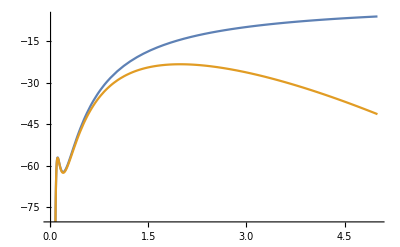

```mathematica
Hfun[n_,g_,R_]:=n/(2 R^2)-n^2/(128π R^3)-(5 n^2)/(16 R)-g √(n R^3);
n=10;
g=1;


Plot[{Hfun[n,0,R],Hfun[n,g,R]},{R,0.01,5}]
```

```mathematica
N/(2m R^2)-N^2/(128 π R^3 Subscript[f, a]^2)-(5 G m^2 N^2)/(16 R)-2 Subscript[g, aγ] √((2 π N R^3)/m)Subscript[F, 0]

H̃=(Ñ)/(2(R̃)^2)-(Ñ)^2/(128 π (R̃)^3)-5/(16 R̃)(Ñ)^2-g̃ √(Ñ (R̃)^3)
```

```mathematica
R=(R̃)/(m Subscript[f, a] √G)
N=Ñ Subscript[f, a]/(m^2 √G)
H=H̃(Subscript[f, a]^3 √G)/m
Subscript[g̃, aγ]=2/(m^2 Subscript[f, a]^4 G^(3/2))Subscript[g, aγ]
```

```mathematica
Subscript[g, aγ]/(10^-11 GeV^-1)(μeV/m)^2((10^12 GeV)/fa)^4 9.1*10^28 Subscript[F, 0]/GeV^4
```

```mathematica
1 GeV^2=10^-3 T
```